```mathematica
path = "/home/koritskiy/rqc/ferrimagnet/confusion_learning/results/2d/2020-08-06-13:21:19/";
X =Transpose[Import[StringJoin[path , "X.dat"]]][[1]];
Y = Transpose[Import[StringJoin[path , "H.dat"]]][[1]];
Zarray = Transpose[Import[StringJoin[path , "Z.dat"]]];
Z = Flatten[Transpose[Zarray]];
XY = Flatten[
Table[
{X[[i]], Y[[j]]},
{i, 1, Length[X]},
{j, 1, Length[Y]}], 
1];
Final = Transpose[Append[Transpose[XY], Z]];
XTicks = Transpose[{Range[Length[X]], N[X, 3]}][[;;;;10]];
YTicks = Transpose[{Range[Length[Y]], N[Y, 3]}][[;;;;10]];
wshape = ListPlot3D[Zarray,
 AxesLabel->{"X", "H", "Accuracy"}, 
ColorFunction->"BlueGreenYellow",
 PlotLegends->Automatic,
 ImageSize->Large,
Ticks->{XTicks,YTicks, Automatic}]
```

-Graphics3D-

```mathematica
Th = Import["/home/koritskiy/rqc/ferrimagnet/crit_fields_0.33-0.35.dat"];
ones = Table[{1}, {i, 1, Dimensions[Th][[1]], 1}];
Th = ListPointPlot3D[Join[Th, ones, 2]];
```

```mathematica
Show[wshape, Th]
```

-Graphics3D-

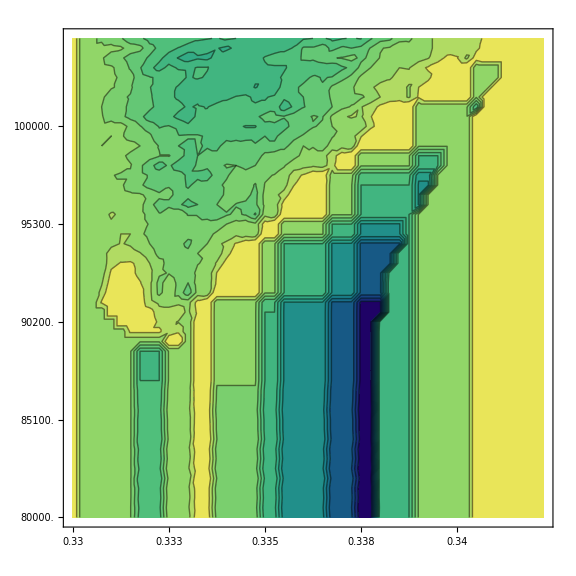

```mathematica
contourPlot = ListContourPlot[
Zarray,
Contours->15,
ColorFunction->"BlueGreenYellow",
ImageSize->Large,
FrameTicks->{XTicks, YTicks}
]
```

```mathematica
GraphicsRow[{wshape, contourPlot}]
```

-Graphics-

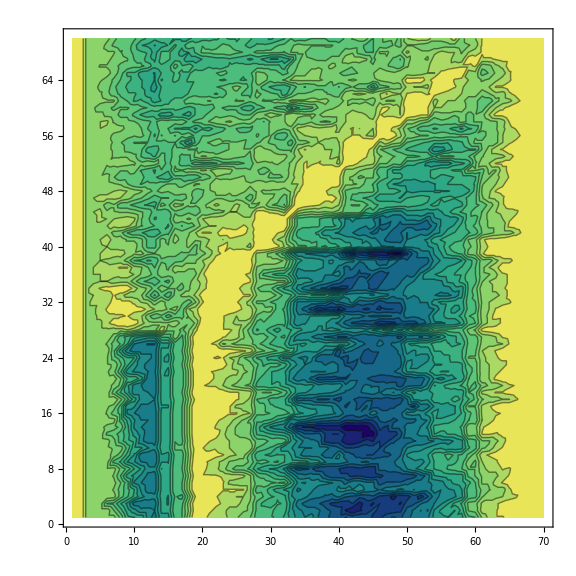

```mathematica
level=0;
d = 0;
u = 70;
contour = Graphics3D[{Texture[contourPlot],EdgeForm[],Polygon[{{d,d,level},{u,d,level},{u,u,level},{d,u,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"]
```

-Graphics3D-